```mathematica
dat=Import[NotebookDirectory[]<>"toplot.dat"];
datn=Select[#,NumberQ]&/@Transpose@dat;Ordering[Length/@datn];
```

```mathematica
ListLinePlot[dat[[;;,5000]],PlotRange->All]
```

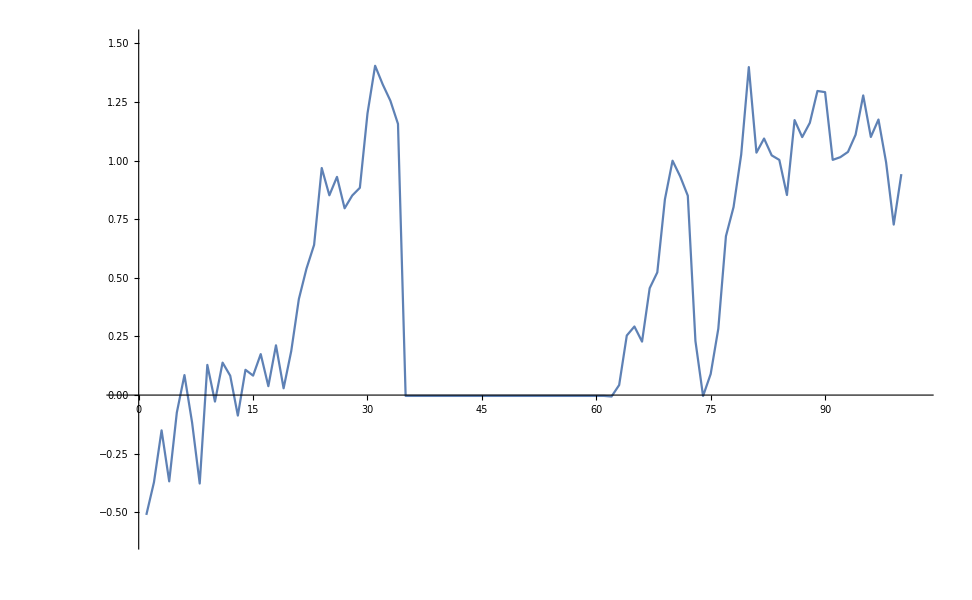

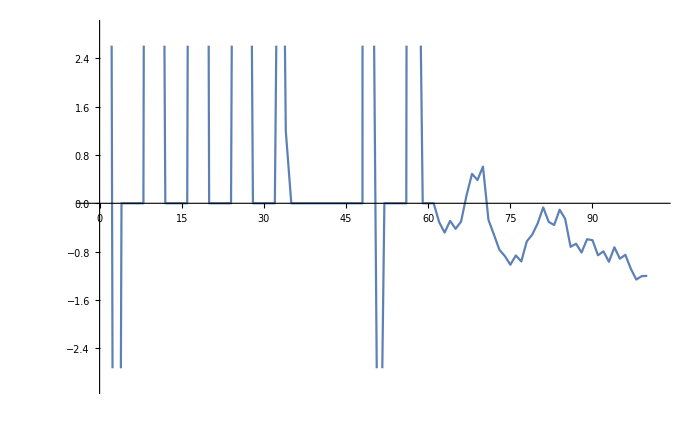

General::munfl: Exp[-1375.97] is too small to represent as a normalized machine number; precision may be lost.

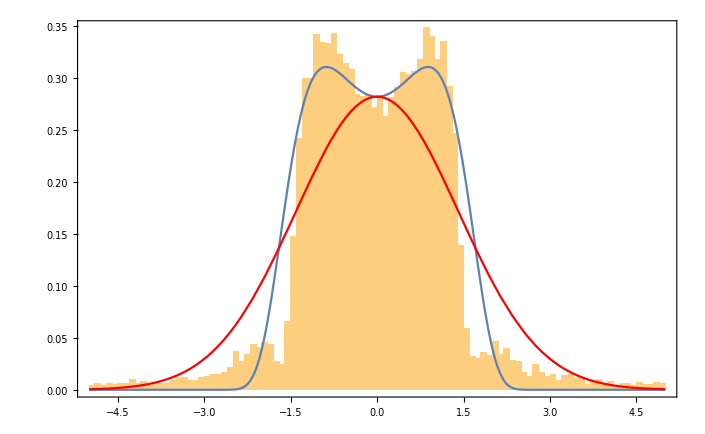

```mathematica
t=200;
a=0.1;
exp=PDF[TransformedDistribution[ArcSinh[a u],u\[Distributed]NormalDistribution[0,√t]],x];
exp2=PDF[NormalDistribution[0,a √t],x];
Show[
Histogram[Flatten[dat[[100;;]]],{-5,5,0.1},"PDF"],
Plot[exp,{x,-5,5},PlotRange->All],
Plot[exp2,{x,-5,5},PlotRange->All,PlotStyle->Red]
,PlotRange->{{-5,5},All},Frame->True,Axes->False]
```

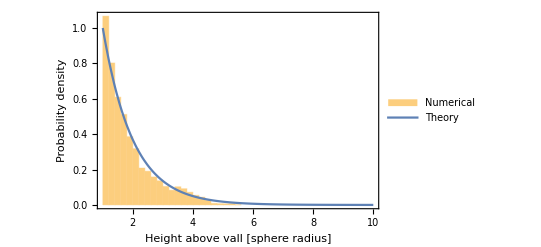

```mathematica
Show[
Histogram[
Select[dat[[;;,17]],#≠0&]
,{1,10,0.2},"PDF",ChartLegends->{"Numerical"}],
Plot[Exp[-(x-1)],{x,1,10},PlotRange->All,PlotLegends->{"Theory"}],
Frame->True,
FrameLabel-> {"Height above vall [sphere radius]","Probability density"}
]
```

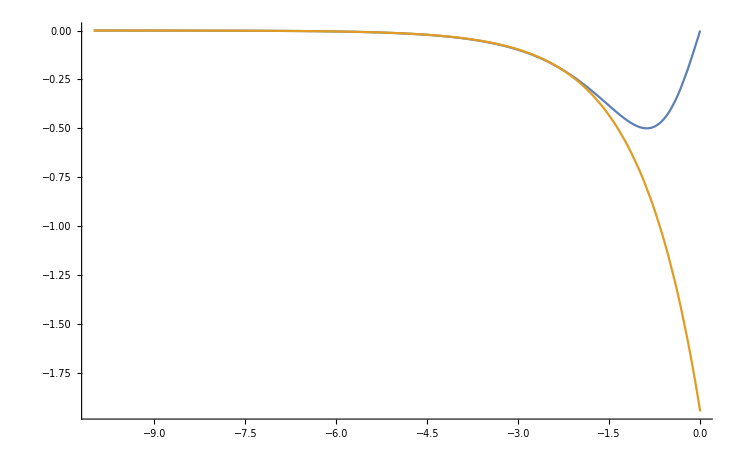

```mathematica
Plot[{Tanh[x]Sech[x],-Exp[x+2/3]},{x,-10,0},PlotRange->All]
```

```mathematica
D[Sech[x],x]//FullSimplify
```

-Sech[x] Tanh[x]

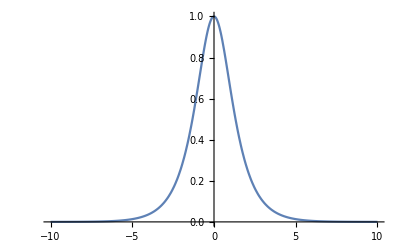

```mathematica
Plot[Sech[x],{x,-10,10}]
```

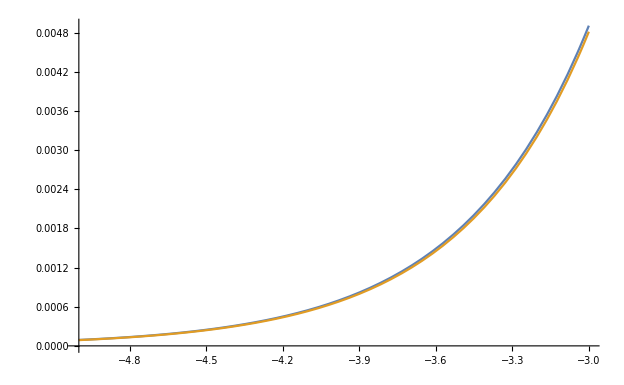

```mathematica
Plot[{-0.5 Tanh[x]Sech[x]Sech[x],0.5 Exp[x+2/3]Sech[x]},{x,-5,-3}]
```